```mathematica
BoxGfx[point_]:=Graphics[Line[{point,point+{0,1},point+{1,1},point+{1,0},point}]];
BoxNetwork[n_]:=Module[{i,points,cp,adj,gfxlist,randparam,t},
t=AbsoluteTime[];
points=Table[{0,0},{i,1,n}];
cp={0,0};
randparam=Floor[n^(2/5)];
Print[AbsoluteTime[]-t];
For[i=2,i≤n,i++,
adj=RandomInteger[{-randparam,randparam}];
If[Mod[i,2]==0,
cp=cp+{0,adj};
,
cp=cp+{adj,0};
];
points[[i]]=cp;
];
Print[AbsoluteTime[]-t];
gfxlist=Table[BoxGfx[points[[i]]],{i,1,n}];
Print[AbsoluteTime[]-t];
Show[gfxlist]
];
```

0.00016

0.00049

0.000737

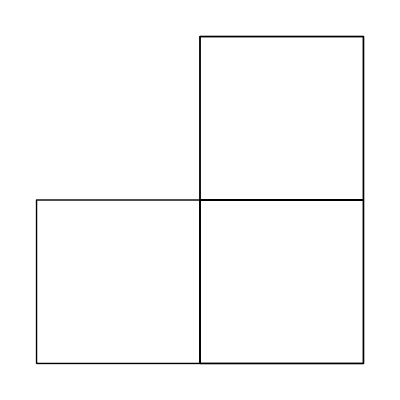

```mathematica
BoxNetwork[5]
```

0.00016

0.000769

0.0013

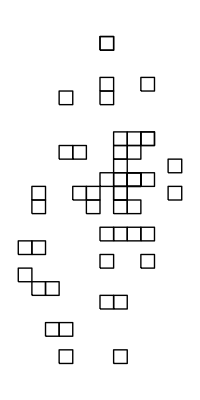

```mathematica
BoxNetwork[50]
```

0.000823

0.00507

0.01045

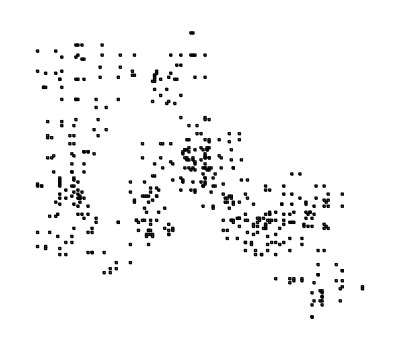

```mathematica
BoxNetwork[500]
```

0.00045

0.035803

0.071407

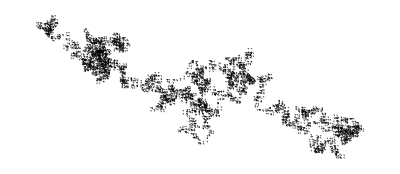

```mathematica
BoxNetwork[5000]
```

```mathematica
BoxNetwork[50000]
```

0.00232

0.376096

0.758566

-Graphics-